```mathematica
Clear["Global`*"];c=2.99792*^8;h=6.626*^-34;
e=1.67*^-19;ϵ0=8.85*^-12;Hart=4.35974*^-18;
au=1.648778*^-41;
```

```mathematica
γgrd={0.543,4.148,0.08,0.67,0.01,0.21,2.04};
ωgrd={17992.007,25068.222,38174.17,40563.97,43659.38,44017.60,28857.014};Egrd={0,0,0,0,0,0,0};
For[i=1,i≤7,i++,
Egrd[[i]]=h*c*(ωgrd[[i]]*100)/Hart;
]
```

```mathematica
αsgrd[ω_]=2/(3*1)*Sum[γgrd[[i]]^2*Egrd[[i]]/(Egrd[[i]]^2-ω^2),{i,1,7}];
```

```mathematica
τ3P0={14/.15,34/.135,376/.639,21/.582,38/.56,15/.35};
ω3P0={15406.253,24326.601,7200.663,22520.281,27022.941,26516.981};
J3P0={1,1,1,1,1,1};
L3P0={0,0,2,2,2,1};
E3P0={0,0,0,0,0,0};
μ3P0={0,0,0,0,0,0};
For[i=1,i≤6,i++,
E3P0[[i]]=h*c*(ω3P0[[i]]*100)/Hart;
μ3P0[[i]]=Sqrt[(2*1+1)*3*1*137^3/(4*(E3P0[[i]])^3)*1/1^2/(τ3P0[[i]]*10^-9/2.41888*^-17)];
]
```

```mathematica
μ3P0
```

{2.08209,0.638805,2.59514,1.89476,1.05115,1.36071}

```mathematica
1/((ω3P0))/100
```

{6.49087×10^-7,4.11073×10^-7,1.38876×10^-6,4.44044×10^-7,3.70056×10^-7,3.77117×10^-7}

```mathematica
αs3P0[ω_]=2/(3*1)*Sum[μ3P0[[i]]^2*(E3P0[[i]])/((E3P0[[i]])^2-ω^2),{i,1,6}];
(*αt3P0[ω_,mF_]=4*(5*1*1/(6*2*3*5))^.5*Sum[(-1)^(1+J3P0[[i]])*(-1)^(1+1+1+1)*(*If[mF≤J3P1[[i]],1,0]*)SixJSymbol[{1,1,J3P0[[i]]},{1,1,2}]*γ3P0[[i]]^2*(E3P0[[i]]-Egrd[[1]])/((E3P0[[i]]-Egrd[[1]])^2-ω^2),{i,1,6}];*)
```

```mathematica
αtot3P0[ω_,F_,mF_,θ_]=αs3P0[ω](*+(3*Cos[θ]^2-1)/2*If[F==1/2,0,(3*mF^2-F*(F+1))/(F*(2F-1))]*αt3P1[ω,mF]*);
```

```mathematica
αtot3P0[.07,1,0,0]
```

7443.53

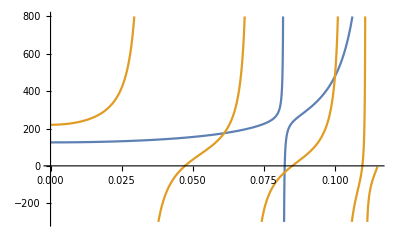

```mathematica
Plot[{αsgrd[ω],αtot3P0[ω,1,0,0],αtot3P1[ω,1,1,0]},{ω,.0,0.115},PlotRange-> {-300,800}]
```

```mathematica
1/18135./100
```

5.5142×10^-7

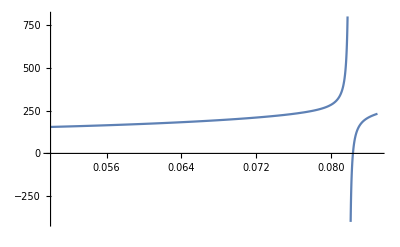

```mathematica
Plot[αsgrd[ω],{ω,0.05,0.085},PlotRange->{-400,800}]
```

```mathematica
(3*mF^2-F*(F+1))/(F*(2F-1))/.F->1/.mF->1
```

1

```mathematica
SixJSymbol[{1,1,2},{1,1,2}]
```

1/30

```mathematica
h*c/(759*^-9)/Hart
```

0.0600301

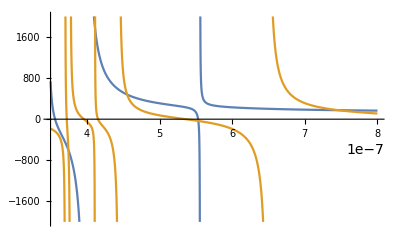

```mathematica
Fx=1/2;mFx=1/2;Plot[{αsgrd[c/ω*h/Hart],αtot3P0[c/ω*h/Hart,Fx,mFx,0]},{ω,350*^-9,800*^-9},PlotRange-> {-2000,2000}]
```

```mathematica
αsgrd[c/759*^-9*h/Hart]
```

172.584

```mathematica
αtot3P0[c/532*^-9*h/Hart,1/2,1/2,0]
```

7.31873

```mathematica
(242-97.3)/242
```

0.597934

```mathematica
(242-7.3)/242
```

0.969835

```mathematica
Jp={0,1,2,2,1,2,2,1,2,2,1,0,1,0, 0,1,2};
```

```mathematica
Lp={0,2,2,2,2,2,2,2,2,2,0,0,0,0,1,1,1};
```

```mathematica
ωp={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
For[k=1,k≤17,k++,
ωp[[1,k]]=c*2Pi*(ω3P1[[k]]-17992.007)*100;
]
```

```mathematica
λp=c/(ωp/(2Pi));
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
For[i=1,i≤17,i++,
λp[[2,i]]=1/(1/λp[[1,i]]+(17288.439*100)-17992.007*100);
λp[[3,i]]=1/(1/λp[[1,i]]+(17288.439*100)-19710.388*100);
]
```

```mathematica
ωp=2*Pi*c/λp;
```

```mathematica
totbr[nt_]:=(Sqrt[(2*Jp[[nt]]+1)*(2*0+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{0,1,1}])^2*ωp[[0+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*1+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{1,1,1}])^2*ωp[[1+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*2+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{2,1,1}])^2*ωp[[2+1,nt]]^3;
```

```mathematica
br[jbr_,nbr_]:=(Sqrt[(2*Jp[[nbr]]+1)*(2*jbr+1)]*SixJSymbol[{Lp[[nbr]],Jp[[nbr]],1},{jbr,1,1}])^2*ωp[[jbr+1,nbr]]^3/totbr[nbr];
```

```mathematica
Sqrt[(2*Jp[[nbr]]+1)*(2*jbr+1)]*SixJSymbol[{Lp[[nbr]],Jp[[nbr]],1},{jbr,1,1}]/.jbr->0/.nbr->15
```

Part::pkspec1: The expression nbr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

0

```mathematica
For[i=2,i≤17,i++,
Print[br[0,i],"\t",br[1,i],"\t",br[2,i]];
]
```

0.647619	0.344391	0.00799026

0.	0.890875	0.109125

0.	0.850132	0.149868

0.58313	0.396385	0.0204843

0.	0.794607	0.205393

0.	0.794154	0.205846

0.578411	0.39994	0.0216488

0.	0.786996	0.213004

0.	0.786934	0.213066

0.153767	0.398195	0.448039

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate	Indeterminate	Indeterminate

0.135976	0.372553	0.491471

Indeterminate	Indeterminate	Indeterminate

0.	1.	0.

0.381612	0.263438	0.35495

0.	0.290283	0.709717

```mathematica
totbr[15]
```

2.98122×10^46

```mathematica
Δ={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
Δ=Abs[ωp]-(2Pi*c/(532*^-9));
```

```mathematica
Γ=γ3P1^2;
```

```mathematica
For[i=1,i≤17,i++,
Print[Γ[[i]]/(Δ[[1,i]])^2*1*^32];
]
```

1463.12

123.045

385.194

7.18376

761.844

2242.91

73.9247

303.867

138.845

36.3886

2024.41

27.3043

121.009

8.93367

592.685

1.85487

378.181

```mathematica
P0[w_]:=186*au*2*.00944/(Pi*w^2)/h
```

```mathematica
P0[1*^-6]
```

27814.8

```mathematica
V[rad_,w_]:=V0*Exp[-2*rad^2/w^2]
```

```mathematica
D[V[rad,w],{rad,2}]
```

V0 ((16 ⅇ^(-(2 rad^2)/w^2) rad^2)/w^4-(4 ⅇ^(-(2 rad^2)/w^2))/w^2)

```mathematica
%/.rad->0
```

-(4 V0)/w^2

```mathematica
m=170.936325*1.6605*^-27;ωt=2Pi*59*^3;P=.009440;ϵ0=8.85419*^-12;
c=2.99792*^8;
au=1.648778*^-41;
```

```mathematica
Solve[{m*ωt^2==4*V0*h/w0^2,V0*h==(186)au/2*2P/(Pi*w0^2)/(1/2*ϵ0*c)/2},{V0,w0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{V0→8.78115×10^6,w0→-7.72437×10^-7},{V0→-8.78115×10^6,w0→0.-7.72437×10^-7 ⅈ},{V0→-8.78115×10^6,w0→0.+7.72437×10^-7 ⅈ},{V0→8.78115×10^6,w0→7.72437×10^-7}}

```mathematica
8.005*^6*h/kB/.kB->1.38*^-23
```

0.000384356

```mathematica
(0.8*^-6)^2/4*m*ωt^2/h
```

9.25372×10^6